# Metodo di Newton

## -Graphics- | Anna Avena Matteo Sanfelici Giulia Cantini Roberto Mizar Nicola Mainetti

## Inizializzazioni e Configurazione

Cliccando su questo tasto andrai ad impostare la directory di lavoro da cui importare il package.

Button[
"Imposta la directory di lavoro",
{
SetDirectory[NotebookDirectory[]],
MessageDialog["Hai impostato la directory di lavoro correttamente"]
},
BaseStyle→{
"GenericButton",
FontFamily→"SourceSansPro",
30
}
]

Imposta la directory di lavoro

Cliccando su questo tasto caricherai il package LearningNewtonsMethod.m

Button[
"Carica Package",
{
Get["LearningNewtonsMethod.m"],
MessageDialog["Hai caricato il package correttamente"]
},
BaseStyle→{
"GenericButton",
FontFamily→"SourceSansPro",
30
}
]

Carica Package

## Problema: Ricerca di uno zero (soluzione) di una funzione

Ti sei mai chiesto come fa la calcolatrice a svolgere calcoli complicati come la radice sesta di 1221?
Questo problema è equivalente alla ricerca di uno zero della funzione f (x) = x^6 - 1221 
oppure della soluzione dell' equazione x^6 - 1221 = 0.

N.B. Una funzione f(x) è una relazione e ha senso considerarla per qualsiasi x che appartiene al suo dominio e quindi non solo per le x che sono zeri della funzione.
	Un’equazione di incognita x invece è un’uguaglianza che risulta vera solo per le particolari x che sono sue soluzioni (dette radici) e non ha senso considerarla per x 		diverse da queste.

### Ma come si trova la scrittura decimale di uno zero di f(x)?

Questo problema potrebbe essere irresolubile se il numero cercato fosse irrazionale e quindi avrebbe infinite cifre decimali.
Siamo però certi che è sempre possibile ottenere un’approssimazione anche con molte cifre decimali di un qualsiasi numero. 
Notando che la funzione f(x)=x^6-1221 è continua e che f(3)<0 e f(4)>0 osservando il grafico risulta chiaro che uno zero di f si troverà tra 3 e 4.

### Second level section heading

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

#### Third level section heading

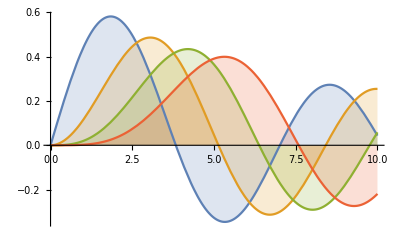

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

### Second level section heading

-Graphics- | SideCaption duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.